```mathematica
f[x_,y_]:=If[(x<0.5)&&(x>0),Return[{2x,y/2}],Return[{2-2x,1-y/2}]]
```

```mathematica
init=Table[{RandomReal[],RandomReal[]},5000];
```

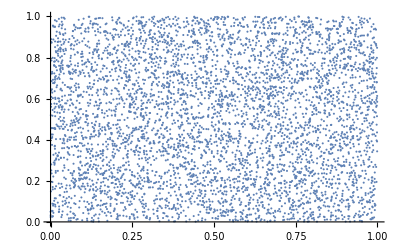

```mathematica
ListPlot[init,PlotRange->{{0,1},{0,1}}]
```

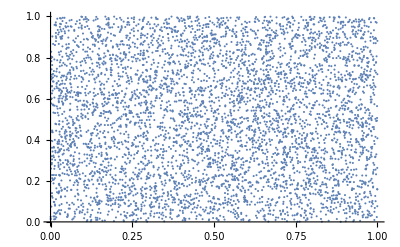
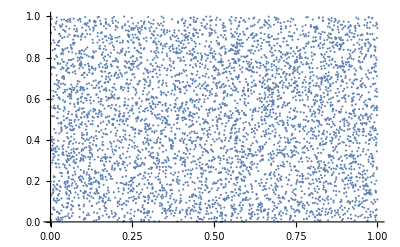
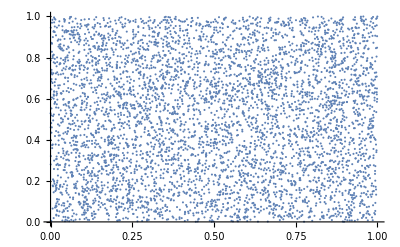
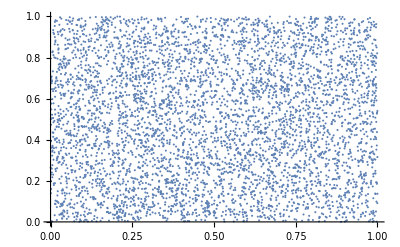
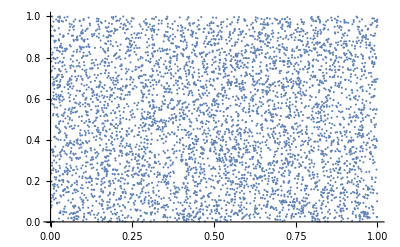
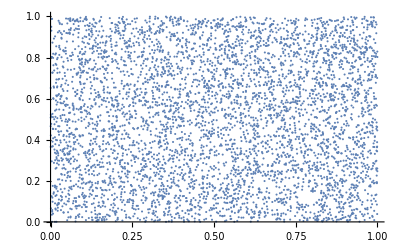
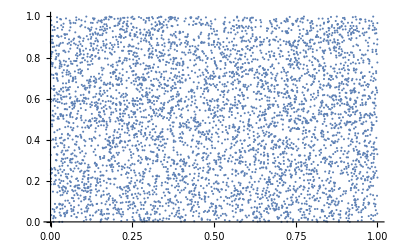
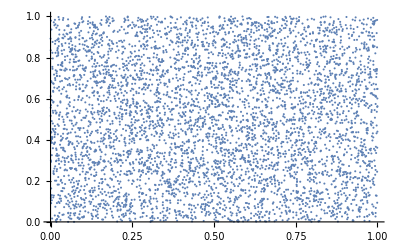
{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
data=init;
Table[{data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];ListPlot[data,PlotRange->{{0,1},{0,1}}]},100]
```